# RotaryEncoderResolution

This notebook demonstrates the “GetRotaryEncoderResolution” code.
Copyright © Terje B. 2006-2011

```mathematica
RotaryEncoderResolution[dolog_, maxelements_] :=
Module[{doLog = dolog, maxElements = maxelements},
curveData = ConstantArray[0, maxElements- Ceiling[maxElements/150]];
resVal = 255;
arrayPos = 0;

For[counter=maxElements, counter >= 4, counter-=Ceiling[maxElements/150],
{
p=Log[counter-2];
arrayPos = arrayPos + 1;
If[ p==0,p=0.1];

	If[doLog == True,
curveData[[arrayPos]]=Round[resVal-(resVal/p)]+30,
curveData[[arrayPos]]=Round[resVal/(maxElements/counter)]
];

If[curveData[[arrayPos]]<1, curveData[[arrayPos]]=1];
	}
];
{curveData, maxElements}
]
```

Test the module:

153

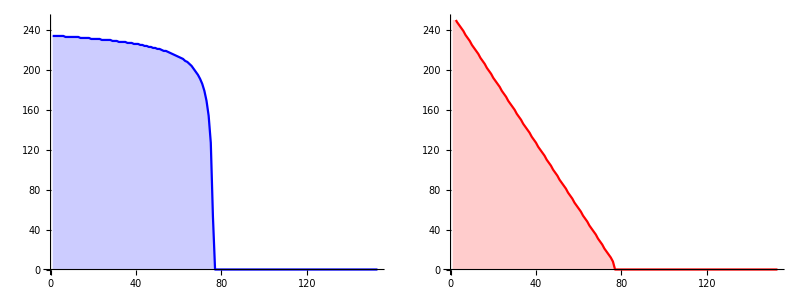

```mathematica
{curveData1, maxElements1} = RotaryEncoderResolution[True, 155];
{curveData2, maxElements2} = RotaryEncoderResolution[False, 155];
Length[curveData2]

g1 = Show[ListLinePlot[curveData1,  PlotStyle->Blue,Filling->Axis, PlotRange->{Automatic, {0, 250}}], ImageSize->Scaled[.40]];
g2 = Show[ListLinePlot[curveData2,  PlotStyle->Red, Filling->Axis, PlotRange->{Automatic, {0, 250}}], ImageSize->Scaled[.70]];
Grid[{{g1, g2}}, ItemSize->{{{25,25}, {25,25}}}, Frame->All, FrameStyle->LightGray]
```

Animate and control the module we’ve created through the MANIPULATE command:

```mathematica
(*strOut = OpenFile[];*) (* Open data file for output *)
mresult = Manipulate[
{curveData,  maxElements} = RotaryEncoderResolution[linlog, maxelements];
g = Show[ListLinePlot[curveData,  PlotStyle->Red, PlotRange->{Automatic, {0, 250}},
ImageSize->Scaled[.8]],AxesLabel->{None, "Pitch"}, Axes->Automatic,AspectRatio->.45,
GridLines->Automatic, GridLinesStyle->LightGray];
Grid[{{g}}, ItemSize->{25}, Frame->None],
(* NOTE: 2nd cell in Grid is not shown {use: g, g}, but ItemSize is set for it (20) *)

 {{linlog, True, "Logarithmic"}, {True, False}, Appearance->{"Labeled", "Open"}},
{{maxelements, 55, "Rotary Encoder Span"}, 4, 255, 1, Appearance->{"Labeled", "Open"}},
SaveDefinitions->False]
```